This notebook produces plots of the orbits generated by local complementation orbit up and including to 9 qubits, when isomorphic graphs are considered equal.

This work refers to “Mapping graph state orbits under local complementation”, https://arxiv.org/abs/1910.03969. Please see this work for assosciated documentation.

You can choose to import from .mx or .csv. Importing data from .mx is faster, but may not be possible on older versions of Mathematica. Importing from .csv is broken up into qubit number as it can be slow for large number of qubits. Feel free to just import the qubit number you are interested in.

## Load data

### Import data from ‘.csv’

#### Init

```mathematica
SetDirectory[NotebookDirectory[]];
goodcolours=ColorData[97,"ColorList"];

(* Graph state display options*)
defcol=ColorData[97,"ColorList"][[7]];
graphsize=100;
vertexsize=0.30;
edgethickness =0.024;
impad=10;

(* precompiled import for csv *)
len4={2,4};
len5={2,6,10,3};
len6={2,6,4,16,10,25,5,5,21,16,2};
len7={2,6,6,16,10,10,16,44,44,14,66,10,10,21,26,36,28,72,114,56,92,57,33,9,46,9};
len8={2,6,6,16,4,16,10,16,44,16,44,10,25,44,44,26,120,66,14,25,120,72,172,10,10,10,21,10,44,66,26,26,28,44,132,114,72,72,198,56,28,10,56,66,72,63,66,176,76,194,352,154,542,300,214,14,66,66,6,57,28,17,72,87,114,372,70,264,542,156,174,542,262,802,117,10,37,36,7,103,46,170,74,340,254,433,476,28,9,39,46,208,298,24,267,4,22,46,28,7,51};
len9={2,6,6,16,6,16,10,10,16,44,16,44,16,16,44,44,44,44,26,120,10,44,44,66,26,66,120,14,44,120,26,44,120,72,120,112,328,72,66,120,328,72,328,174,18,196,464,10,16,10,21,16,44,66,26,36,26,44,26,28,44,132,114,5,44,72,44,28,72,132,26,120,372,72,72,75,56,28,56,44,26,66,132,114,176,120,28,120,72,66,120,372,352,76,542,56,176,352,154,120,176,42,72,76,72,154,372,352,196,542,300,76,120,352,72,328,194,198,194,484,542,300,984,66,46,74,328,208,352,968,542,300,984,1498,828,154,91,240,488,420,1428,498,5,36,132,66,75,66,114,14,204,24,57,28,87,72,132,26,72,372,114,372,114,112,542,264,94,87,132,198,176,46,198,264,372,1052,91,156,542,174,38,72,132,352,204,186,198,528,220,1052,296,300,754,754,76,194,188,352,28,220,372,372,1052,544,324,1008,312,1052,1052,1052,1056,1550,1534,220,186,1476,1498,924,763,156,308,98,542,272,300,984,754,3004,222,426,105,1436,704,1472,474,1508,1498,2104,4246,1328,28,37,21,89,14,46,57,186,170,142,170,74,340,76,204,198,102,542,306,320,484,782,38,36,204,220,198,372,542,1052,340,1052,1096,1594,94,192,178,476,542,596,920,3004,952,1544,806,202,1334,156,504,528,1052,462,340,192,542,542,476,1534,754,484,1564,952,1534,1550,1550,3004,1578,116,58,452,283,462,3088,908,399,2198,4306,4402,2270,2292,4378,2684,9,63,100,46,42,75,85,174,340,119,182,188,1578,460,220,166,1148,24,24,170,160,784,564,168,494,1536,1594,1610,1578,768,494,1568,476,1610,1626,124,484,1114,1628,814,1594,66,952,356,952,126,840,2214,4470,818,2262,8836,726,1129,1384,1398,305,844,4514,2336,476,153,27,70,46,162,170,276,340,220,494,1610,128,494,988,736,1348,227,608,1246,541,4580,4538,1384,2408,744,4594,4592,2366,344,870,119,115,99,30,269,538,238,68,772,1216,630,1414,672,836,4670,80,1464,1478,862,278,129,94,893,609,242,21,567};

lenorbitsCi={{1},{1},{1},len4,len5,len6,len7,len8,len9};


fourCiorbits=Range[2];
fourCigraphlists=Table[0,{i,Range[2]},{j,len4[[i]]}];
four=4;

fiveCiorbits=Range[4];
fiveCigraphlists=Table[0,{i,Range[4]},{j,len5[[i]]}];
five=5;

sixCiorbits=Range[11];
sixCigraphlists=Table[0,{i,Range[11]},{j,len6[[i]]}];
six=6;

sevenCiorbits=Range[26];
sevenCigraphlists=Table[0,{i,Range[26]},{j,len7[[i]]}];
seven=7;

eightCiorbits=Range[101];
eightCigraphlists=Table[0,{i,Range[101]},{j,len8[[i]]}];
eight=8;

nineCiorbits=Range[440];
nineCigraphlists=Table[0,{i,Range[440]},{j,len9[[i]]}];
nine=9;

rwdgraphs={{0},{0},{0},{1,1},{1,1,1,2},{1,1,1,1,1,1,1,1,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,2,2,2,1,2,2,1,1,2,1,2,2,1,2,1,2,2,2,2,2,2,2,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,2,2,1,1,2,1,1,2,2,1,1,2,1,1,2,2,1,2,1,1,1,2,2,2,1,1,1,2,1,1,2,2,1,2,2,2,2,2,1,2,1,1,1,2,2,2,2,1,2,2,1,1,2,1,1,2,2,2,2,2,2,2,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,1,2,1,2,1,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,3,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,3,2,3,3,2,3,2,3,3,3,2,2,2,2,2,2,2,2,2,2,2,3,3,2,3,3,3,2,2,2,3,2,2,3,3,3,2,2,3}};
```

#### 4 qubit

```mathematica
fourCidat=ToString@Import["4qubitorbitsCi.csv"];
fourCidat=StringReplace[fourCidat,"("->"{"];
fourCidat=StringReplace[fourCidat,")"->"}"];
fourCidat=StringReplace[fourCidat,"-"->"->"];
fourCidat=ToExpression@fourCidat;

Do[
fourCiorbits[[i]]=Graph[
Range[fourCidatᵀ[[2]][[i]]],
fourCidatᵀ[[3]][[i]],EdgeLabels->Thread[fourCidatᵀ[[4]][[i]]ᵀ[[1]]->fourCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fourCiorbits}];

Do[
fourCigraphlists[[i]][[j]]=Graph[
Range[four],
fourCidat[[i]][[5]][[j]]
];
fourCigraphlists[[i]][[j]]=UndirectedGraph[fourCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fourCidat},{j,Length@fourCidat[[i]][[5]]}];
```

#### 5 qubit

```mathematica
fiveCidat=ToString@Import["5qubitorbitsCi.csv"];
fiveCidat=StringReplace[fiveCidat,"("->"{"];
fiveCidat=StringReplace[fiveCidat,")"->"}"];
fiveCidat=StringReplace[fiveCidat,"-"->"->"];
fiveCidat=ToExpression@fiveCidat;

Do[
fiveCiorbits[[i]]=Graph[
Range[fiveCidatᵀ[[2]][[i]]],
fiveCidatᵀ[[3]][[i]],EdgeLabels->Thread[fiveCidatᵀ[[4]][[i]]ᵀ[[1]]->fiveCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fiveCiorbits}];

Do[
fiveCigraphlists[[i]][[j]]=Graph[
Range[five],
fiveCidat[[i]][[5]][[j]]
];
fiveCigraphlists[[i]][[j]]=UndirectedGraph[fiveCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fiveCidat},{j,Length@fiveCidat[[i]][[5]]}];
```

#### 6 qubit

```mathematica
sixCidat=ToString@Import["6qubitorbitsCi.csv"];
sixCidat=StringReplace[sixCidat,"("->"{"];
sixCidat=StringReplace[sixCidat,")"->"}"];
sixCidat=StringReplace[sixCidat,"-"->"->"];
sixCidat=ToExpression@sixCidat;

Do[
sixCiorbits[[i]]=Graph[
Range[sixCidatᵀ[[2]][[i]]],
sixCidatᵀ[[3]][[i]],EdgeLabels->Thread[sixCidatᵀ[[4]][[i]]ᵀ[[1]]->sixCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sixCiorbits}];

Do[
sixCigraphlists[[i]][[j]]=Graph[
Range[six],
sixCidat[[i]][[5]][[j]]
];
sixCigraphlists[[i]][[j]]=UndirectedGraph[sixCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sixCidat},{j,Length@sixCidat[[i]][[5]]}];
```

#### 7 qubit

```mathematica
sevenCidat=ToString@Import["7qubitorbitsCi.csv"];
sevenCidat=StringReplace[sevenCidat,"("->"{"];
sevenCidat=StringReplace[sevenCidat,")"->"}"];
sevenCidat=StringReplace[sevenCidat,"-"->"->"];
sevenCidat=ToExpression@sevenCidat;

Do[
sevenCiorbits[[i]]=Graph[
Range[sevenCidatᵀ[[2]][[i]]],
sevenCidatᵀ[[3]][[i]],EdgeLabels->Thread[sevenCidatᵀ[[4]][[i]]ᵀ[[1]]->sevenCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sevenCiorbits}];

Do[
sevenCigraphlists[[i]][[j]]=Graph[
Range[seven],
sevenCidat[[i]][[5]][[j]]
];
sevenCigraphlists[[i]][[j]]=UndirectedGraph[sevenCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sevenCidat},{j,Length@sevenCidat[[i]][[5]]}];
```

#### 8 qubit (takes a few minutes)

```mathematica
eightCidat=Import["8qubitorbitsCi.csv"];
Print["Import successfull. Converting to string for processing.."];
eightCidat=ToString@eightCidat;
Print["Success! Processing string.."];
eightCidat=StringReplace[eightCidat,"("->"{"];
eightCidat=StringReplace[eightCidat,")"->"}"];
eightCidat=StringReplace[eightCidat,"-"->"->"];
eightCidat=ToExpression@eightCidat;
Print["Success! Generating orbits.."];

Do[
eightCiorbits[[i]]=Graph[
Range[eightCidatᵀ[[2]][[i]]],
eightCidatᵀ[[3]][[i]],EdgeLabels->Thread[eightCidatᵀ[[4]][[i]]ᵀ[[1]]->eightCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@eightCiorbits}];

Do[
eightCigraphlists[[i]][[j]]=Graph[
Range[eight],
eightCidat[[i]][[5]][[j]]
];
eightCigraphlists[[i]][[j]]=UndirectedGraph[eightCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@eightCidat},{j,Length@eightCidat[[i]][[5]]}];

Print["Success! Done."];
```

Import successfull. Converting to string for processing..

Success! Processing string..

Success! Generating orbits..

Success! Done.

#### 9 qubit (takes tens of minutes)

```mathematica
nineCidat=Import["9qubitorbitsCi.csv"];
Print["Import successfull. Converting to string for processing.."];
nineCidat=ToString@nineCidat;
Print["Successfull. Processing string.."];
nineCidat=StringReplace[nineCidat,"("->"{"];
nineCidat=StringReplace[nineCidat,")"->"}"];
nineCidat=StringReplace[nineCidat,"-"->"->"];
nineCidat=ToExpression@nineCidat;
```

Import successfull. Converting to string for processing..

Successfull. Processing string..

```mathematica
Print["Success! Generating orbits.."];
Do[
nineCiorbits[[i]]=Graph[
Range[nineCidatᵀ[[2]][[i]]],
nineCidatᵀ[[3]][[i]],EdgeLabels->Thread[nineCidatᵀ[[4]][[i]]ᵀ[[1]]->nineCidatᵀ[[4]][[i]]ᵀ[[2]]]];
,{i,Length@nineCiorbits}];

Print["Success! Generating graphlist.."];
Do[
nineCigraphlists[[i]][[j]]=Graph[
Range[nine],
nineCidat[[i]][[5]][[j]]
];
nineCigraphlists[[i]][[j]]=UndirectedGraph[nineCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@nineCidat},{j,Length@nineCidat[[i]][[5]]}];
Print["Success! Done."];
```

Success! Generating orbits..

Success! Generating graphlist..

Success! Done.

#### Initialise to one variable.

```mathematica
orbitsCi={{},{},{},fourCiorbits,fiveCiorbits,sixCiorbits,sevenCiorbits,eightCiorbits,nineCiorbits};
orbitsCigraphlist={{},{},{},fourCigraphlists,fiveCigraphlists,sixCigraphlists,sevenCigraphlists,eightCigraphlists,nineCigraphlists};

ClearAll[fourCidat,fiveCidat,sixCidat,sevenCidat,eightCidat,nineCidat,fourCiorbits,fiveCiorbits,sixCiorbits,sevenCiorbits,eightCiorbits,nineCiorbits,fourCigraphlists,fiveCigraphlists,sixCigraphlists,sevenCigraphlists,eightCigraphlists,nineCigraphlists];
```

### Import data from ‘.mx’ (much faster)

#### Import from Mathematica 11 ‘.mx’ file (this may take 30s)

```mathematica
SetDirectory[NotebookDirectory[]];
orbitsCi=Import["orbitsCi.mx"];
orbitsCigraphlist=Import["orbitsCigraphlist.mx"];
```

## Functions

```mathematica
deleteIsoG1[gl_List]:=Module[{},DeleteDuplicates[gl,IsomorphicGraphQ]];

colourblender[one_,two_]:=Blend[{one,two},0.5]; 


plotOrbitCi[noqub_,myclass_,embed_: "SpringElectricalEmbedding"]:=Module[{oedgelabels,theselabels,graphimgs,imsz,g1,graphlabelgraph,graphlabels,thisorbit},(* Sanitise graphs for printing *)
Do[orbitsCigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];

(* get images of each graph state to plot on the vertices of the orbit *)
graphimgs=Range@Length@orbitsCigraphlist[[noqub]][[myclass]];
imsz=100;
Do[
(* graph state vertices labelled? *)
If[graphsvertexlabelledQ,g1=Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],VertexLabels->Thread[Range[noqub]->Range[noqub]],VertexSize->svsize,EdgeStyle->sesize,VertexLabelStyle->Directive[Black,vertexlabelfontsize]];
g1=SetProperty[g1,VertexLabels->(#->Placed[#2,{0.59,0.4}]&@@@(VertexLabels/.Options[g1]))];
,
g1=Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],VertexSize->svsize,EdgeStyle->sesize];
];
graphimgs[[i]] = Show[{g1,
Graphics[{Directive[Black,Thickness[gcirclethickness]],Circle[{0,0},gpadding]}]},ImageSize->imsz]
,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
graphlabelgraph=Thread[Range[Length@orbitsCigraphlist[[noqub]][[myclass]]]->graphimgs];

(* compute graph state labels *)
If[graphslabelledQ ,
graphlabels= Table[i->"G"<>ToString[i],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}],
graphlabels=Thread[Range@Length@orbitsCigraphlist[[noqub]][[myclass]]->Table[None,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}]];
];


If[orbitedgeslabelledQ,
thisorbit=Graph[orbitsCi[[noqub]][[myclass]],VertexLabels->graphlabels,EdgeLabels->oedgelabels,VertexShape->graphlabelgraph,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize],GraphLayout->embed];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];];
,
thisorbit=UndirectedGraph[orbitsCi[[noqub]][[myclass]],EdgeLabels->None,VertexShape->graphlabelgraph,VertexLabels->graphlabels,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize],GraphLayout->embed];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];];
];

thisorbit];



plotOrbitMatrixCi[noqub_,myclass_]:=Module[{theselabels,oedgelabels,goodcolours,labels,colourlabel,mycolours,isocolours,isocolours2,gatheredisocols,isolens,isocount,colourisoadjmat,LCadj,isogroups,isomat,one,two,glo,glr,glos,bticks,arfaccumisolenssd,tickas,gl,btickstr,accumisolens,noedg,orbitadj,orbitlegend,dist,distp,distleg},


(* Sanitise graphs for printing *)
Do[orbitsCigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];


(*compute colour space*)
goodcolours=ColorData[97,"ColorList"];
labels=ToExpression[theselabelsᵀ[[2]]];

(*one colour per LC type (graph state vertex) *)
colourlabel=Flatten[labels/.{Thread[Range[15]->goodcolours]},1];
colourlabel={Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels])ᵀ[[1]],colourlabel}ᵀ;

(*Isomorphic region colours*)
mycolours=Table[Hue[i/Length[orbitsCigraphlist[[noqub]][[myclass]]],satmod,brightmod],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
isocolours=mycolours;


(*Find regions of isomorphic graphs, set colour regions to 'isocolours'*)
Do[
Do[
If[SameQ[(Length@EdgeList@orbitsCigraphlist[[noqub]][[myclass]][[i]]),(Length@EdgeList@orbitsCigraphlist[[noqub]][[myclass]][[j]])],
isocolours[[j]]=mycolours[[i]];
]
,{j,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];


(*define colours for regions of isomorphic graphs*)
isocolours2=Outer[colourblender,isocolours,isocolours];
gatheredisocols=isocolours2;
Do[
gatheredisocols[[i]]=Gather[isocolours2[[i]]],
{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
isolens=Range[Length@gatheredisocols[[1]]];
Do[isolens[[i]]=Length@gatheredisocols[[1]][[i]],{i,Length@gatheredisocols[[1]]}];
isocount=Flatten[Table[j,{j,Length@isolens},{i,isolens[[j]]}]];


(*regions of same number of edges: 'gatheredisocols'*)
Do[
Do[gatheredisocols[[i]][[j]][[k]]=Blend[{gatheredisocols[[i]][[j]][[k]],Hue[0.95,0.0,1]},1*Abs[isocount[[i]]-j]/Length@gatheredisocols[[i]]],{k,Length@gatheredisocols[[i]][[j]]}];
,{i,Length@gatheredisocols},{j,Length@gatheredisocols[[i]]}];
Do[gatheredisocols[[i]]=Flatten[gatheredisocols[[i]]],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];


(*varible to plot: 'colourisoadjmat'*)
colourisoadjmat=AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]] //Normal;
Do[colourisoadjmat[[i]][[j]]=colourisoadjmat[[i]][[j]]+gatheredisocols[[i]][[j]],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]},{j,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
isogroups=colourisoadjmat;

Do[
one=colourlabel[[i]][[1]][[1]];
two=colourlabel[[i]][[1]][[2]];
If[
ToString[Head@colourlabel[[i]][[2]]]≠"List",
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]],
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]][[1]]]
,{i,Length@colourlabel}];



(*Make frame ticks*)
glo=Accumulate@isolens;
glr=glo;
glos=ToString/@glo;
accumisolens=Accumulate[isolens];
bticks=(Accumulate@isolens +Delete[ Flatten[PrependTo[accumisolens,0]],-1]) / 2;
noedg = Length/@EdgeList/@orbitsCigraphlist[[noqub]][[myclass]]//DeleteDuplicates;
btickstr=ToString/@noedg;
Do[
If[
Abs[bticks[[i+1]]-bticks[[i]]]<tickthresedge,
btickstr[[i]]=""
],{i,Length@bticks-1}];
Do[
If[
Abs[glo[[i+1]]-glo[[i]]]<tickthresno,
glos[[i]]=""
],{i,Length@glo-1}];
tickas={{glo+1/2,glos}ᵀ,{bticks+1/2,btickstr}ᵀ,None,{glo+1/2,glos}ᵀ};
gl={glr,Length@orbitsCigraphlist[[noqub]][[myclass]]-glr};



orbitadj=ArrayPlot[colourisoadjmat,
MaxPlotPoints->Length@AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
ImagePadding->40,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize];

orbitlegend=TableForm[{Range[noqub],goodcolours[[1;;noqub]]}ᵀ];

dist=Table[0,{i,9},{j,Length/@orbitsCigraphlist[[i]]}];
dist[[noqub]][[myclass]]=GraphDistanceMatrix[orbitsCi[[noqub]][[myclass]]];

distp=MatrixPlot[dist[[noqub]][[myclass]],
MaxPlotPoints->Length@AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize,
ImagePadding->40,
ColorFunction->"SolarColors"];

distleg=BarLegend[{"SolarColors",{0,1+Max@dist[[noqub]][[myclass]]}},Max@dist[[noqub]][[myclass]],Method->{TicksStyle->Black,LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize}} ];

{orbitadj,orbitlegend,distp,distleg}];
```

# Print unlabelled graph state orbits, C_i

#### Plot settings

```mathematica
sesize = Thickness[0.004];(*graph state edge size*)
lesize =Thickness[0.004];(*orbit edge size*)
svsize=0.4; (*graph state vertex size*)
lvsize=0.6; (*orbit vertex size*)
gcirclethickness=0.02;(*thickness of orbit vertex circumference*)
gpadding=1.6;(*padding of graph states*)
edgefontsize=12;(*orbit edge font size*)
vertexlabelfontsize=8;(*graph state vertex font size*)

(* Label edge vertices when printing orbit as a graph?*)
orbitedgeslabelledQ=False;   
graphslabelledQ=False;
graphsvertexlabelledQ=False;
```

#### Pick and display a graph state orbit

First graph in orbit is: -Graphics-

Number of graphs in Orbit is: 25

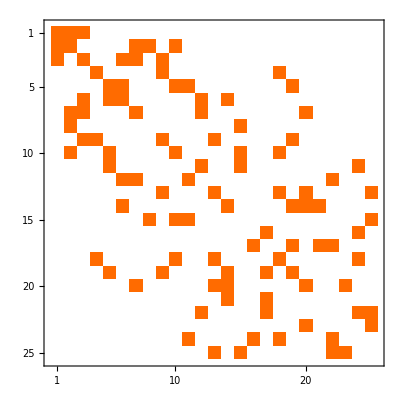
Adjacency matrix of orbit is: -Graphics-

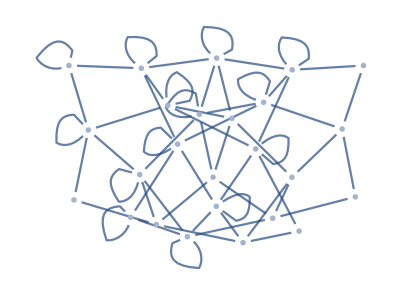

```mathematica
noqub=6;
myclass=6;

Print["First graph in orbit is: ",orbitsCigraphlist[[noqub]][[myclass]][[1]]]
Print["Number of graphs in Orbit is: ",Length@orbitsCigraphlist[[noqub]][[myclass]]]
Print["Adjacency matrix of orbit is: ",MatrixPlot@AdjacencyMatrix@orbitsCi[[noqub]][[myclass]]]

plotOrbitCi[noqub,myclass,"SpringElectricalEmbedding"]
```

## Print unlabelled graph state orbit adjacency matrices, ordered and grouped by edgecount

#### Plot Settings

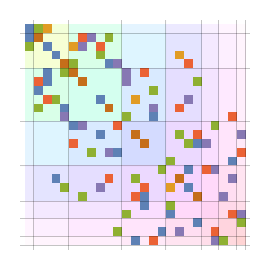
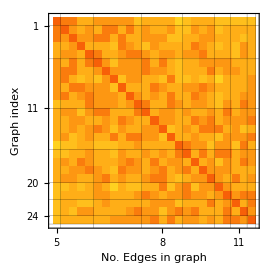
{-Graphics-,1 | RGBColor[0.368417, 0.506779, 0.709798]
2 | RGBColor[0.880722, 0.611041, 0.142051]
3 | RGBColor[0.560181, 0.691569, 0.194885]
4 | RGBColor[0.922526, 0.385626, 0.209179]
5 | RGBColor[0.528488, 0.470624, 0.701351]
6 | RGBColor[0.772079, 0.431554, 0.102387],-Graphics-,}

```mathematica
(*Adjust plot cosmetics*)
myframethickness=0.5;
myfontsize=10;
graphsize=270;

(*Adjust colour space for plots*)
satmod=0.17;
brightmod=1;

(*Difference in edge number required to be displayed on the plot*)
tickthresno=1;          (*in graph index*)
tickthresedge=1;     (*in edge number*)

plotOrbitMatrixCi[noqub,myclass]
```